```mathematica
path="/home/abduld/Dropbox/wbGPU/grader/dbReader/programs";
```

```mathematica
path="/tmp/programs";
```

```mathematica
progs=Import[path,"Text"];
progs=StringSplit[progs,"\n"];
```

```mathematica
loc[prog_]:=Length[StringSplit[prog,"\\n"]]
```

```mathematica
sprogs=SortBy[progs,loc];
```

```mathematica
Manipulate[sprogs[[ii]]//ToExpression,{ii,1,Length[sprogs],1}]
```

```mathematica
Mean[StringLength/@progs]//N
```

2690.26

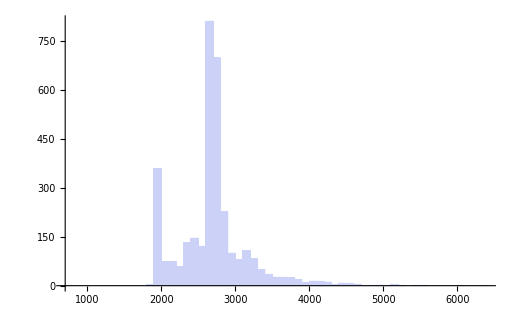

```mathematica
Histogram[StringLength/@progs]
```